```mathematica
EmpiricData = {
{0,2},{1,2},{2,3},{3,3},{4,9},{5,14},{6,18},{7,21},{8,29},{9,41},{10,55},{11,79},{12,104},{13,131},{14,182},{15,246},{16,302},{17,504},{18,655},{19,860},{20,1016},{21,1332},{22,1646},{23,2053},{24,2388},{25,2814},{26,3244},{27,3924},{28,4876},{29,5560},{30,6398},{31,7399},{32,7995},{33,8536},{34,9377},{35,9974}, {36, 10482}, {37, 10865}
};
```

```mathematica
LogisticModel = a/(1 + b*Exp[-c ( x - d)]);
```

```mathematica
LogisticModelFitParameter = FindFit[EmpiricData, LogisticModel, {a, b, c, d}, x]
```

{a→12876.1,b→49.5191,c→0.24742,d→14.2908}

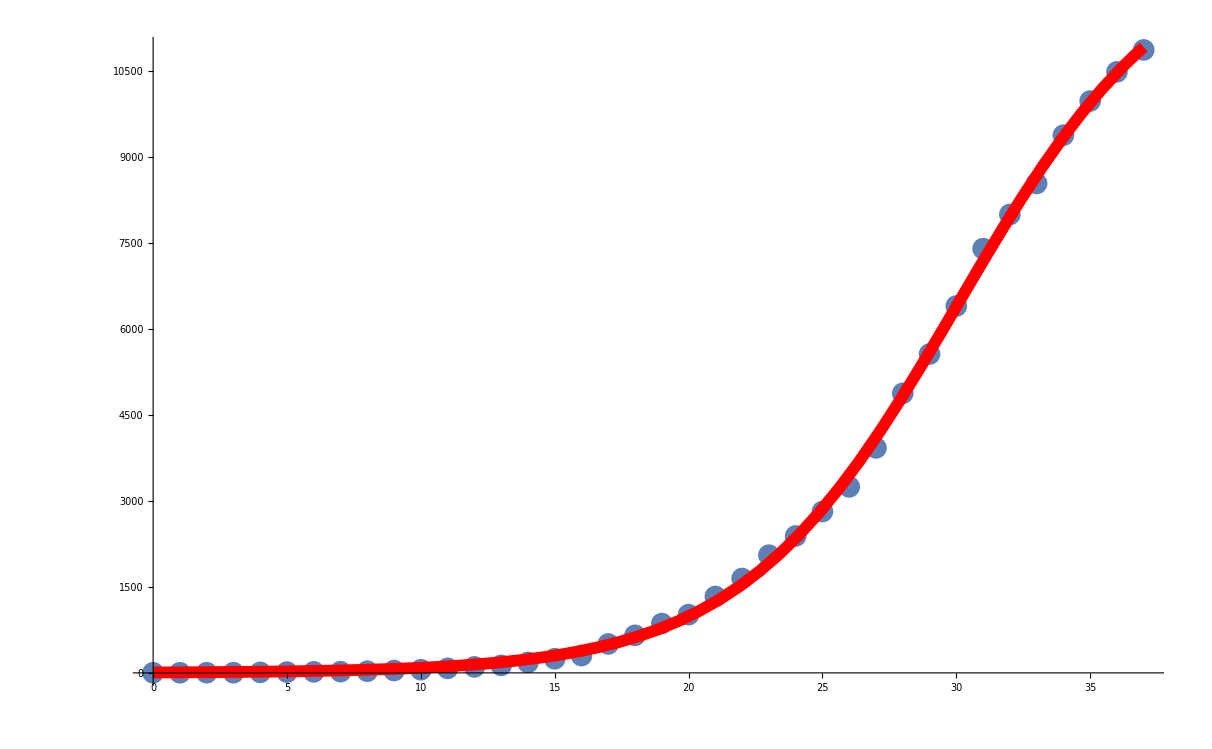

```mathematica
Show[{ListPlot[EmpiricData], Plot[LogisticModel /. LogisticModelFitParameter, {x, 0, 37}, PlotStyle -> {Red, Thickness[0.007]}, PlotRange -> All]}]
```

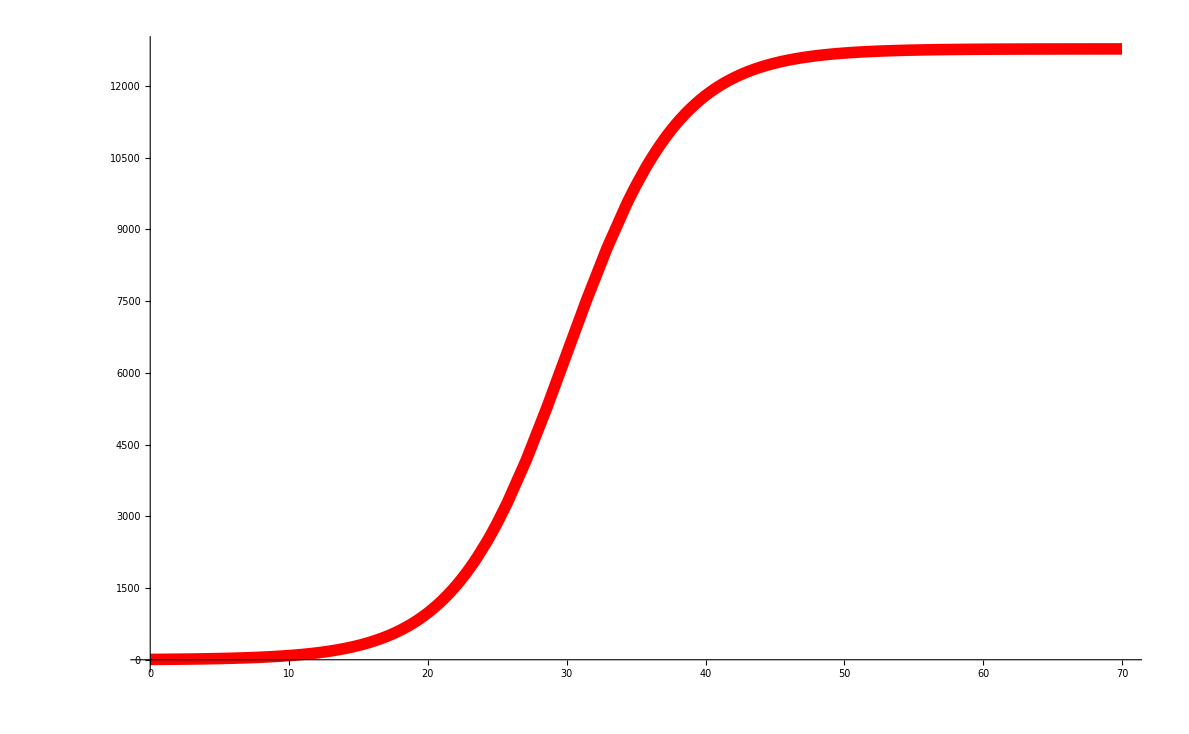

```mathematica
Plot[LogisticModel /. LogisticModelFitParameter, {x, 0, 70}, PlotStyle -> {Red, Thickness[0.007]}, PlotRange -> All]
```